```mathematica
ClearAll["Global`*"]
$RecursionLimit=10000000
```

10000000

```mathematica
cc:=cc=CoefficientList[Series[ x/Log[1-x],{x,0,20}],x]
d2[n_,k_]:=d2[n,k]=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1
D2[n_,k_]:=D2[n,k]=D2[n-1,k]+d2[n,k];D2[1,k_]:=0
K[n_]:=K[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
k2[n_,k_]:=k2[n,k]=Sum[k2[j,k-1] k2[n/j,1],{j,Divisors[n]}];k2[n_,1]:=K[n];k2[1,1]:=0;k2[n_,0]:=0;k2[1,0]:=1
K2[n_,k_]:=K2[n,k]=K2[n-1,k]+k2[n,k];K2[1,k_]:=0
e2[n_,1]:=e2[n,1]=Sum[ cc[[k+1]] k2[n,k],{k,0,Log[2,n]}];e2[1,1]:=0;
e2[n_,k_]:=Sum[e2[j,k-1]e2[n/j,1],{j,Divisors[n]}];e2[n_,0]:=0;e2[1,0]:=1
E2[n_,k_] := E2[n,k] = E2[n-1,k]+e2[n,k];E2[1,k_]:=0
```

```mathematica
DiscretePlot[ {n,E2[n,1],E2[n,2],E2[n,3],E2[n,4],E2[n,5],E2[n,6],E2[n,7],E2[n,8]},{n,1,10000}]
DiscretePlot[ {n,D2[n,1],D2[n,2],D2[n,3],D2[n,4],D2[n,5],D2[n,6],D2[n,7],D2[n,8]},{n,1,10000}]
DiscretePlot[ {n,K2[n,1],K2[n,2],K2[n,3],K2[n,4],K2[n,5], ,K2[n,6],K2[n,7],K2[n,8]},{n,1,10000}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Series[ Log[x+1]/Log[1-Log[x+1]],{x,0,20}]
```

-1+x/2-x^2/6+x^3/8-(61 x^4)/720+(5 x^5)/72-(3379 x^6)/60480+(829 x^7)/17280-(37501 x^8)/907200+(265723 x^9)/7257600-(15650779 x^10)/479001600+(16097 x^11)/544320-(23499108071 x^12)/871782912000+(1994072953 x^13)/80472268800-(179760855523 x^14)/7846046208000+(27293443733 x^15)/1280987136000-(212398886231569 x^16)/10670622842880000+(325618047593 x^17)/17435658240000-(898455354657922519 x^18)/51090942171709440000+(89350786286831273 x^19)/5377993912811520000-(132709572856375410013 x^20)/8430005458332057600000+O[x]^21

```mathematica
FullSimplify[Log[x+1]/Log[1-Log[x+1]]]
```

Log[1+x]/Log[1-Log[1+x]]

```mathematica
Series[ x/Log[1-x],{x,0,20}]
```

-1+x/2+x^2/12+x^3/24+(19 x^4)/720+(3 x^5)/160+(863 x^6)/60480+(275 x^7)/24192+(33953 x^8)/3628800+(8183 x^9)/1036800+(3250433 x^10)/479001600+(4671 x^11)/788480+(13695779093 x^12)/2615348736000+(2224234463 x^13)/475517952000+(132282840127 x^14)/31384184832000+(2639651053 x^15)/689762304000+(111956703448001 x^16)/32011868528640000+(50188465 x^17)/15613165568+(2334028946344463 x^18)/786014494949376000+(301124035185049 x^19)/109285437800448000+(12365722323469980029 x^20)/4817145976189747200000+O[x]^21

```mathematica
tt:= tt = CoefficientList[Series[ Log[x+1]/Log[1-Log[x+1]],{x,0,20}],x]
```

```mathematica
tt[[4]]
```

1/8

```mathematica
E2[100,1]
```

262613/8640

```mathematica
Sum[ tt[[k+1]] D2[100,k],{k,0,Log[2,100]}]
```

262613/8640

```mathematica
t2:= t2=CoefficientList[Series[ (Log[x+1]/Log[1-Log[x+1]]),{x,0,20}],x]
```

```mathematica
Sum[ t2[[k+1]] D2[100,k],{k,0,Log[2,100]}]
```

262613/8640

```mathematica
E2[100,2]
```

338761/8640

```mathematica
Plot[{Re[Log[x+1]/Log[1-Log[x+1]]],Im[Log[x+1]/Log[1-Log[x+1]]]},{x,1,10000000000000000}]
```

-Graphics-

```mathematica
N[Log[1+x]/Log[1-Log[1+x]]/.x->4]
```

-0.0787973-0.499879 ⅈ

```mathematica
CoefficientList[Series[ (x/Log[1-x]),{x,0,20}],x]
```

{-1,1/2,1/12,1/24,19/720,3/160,863/60480,275/24192,33953/3628800,8183/1036800,3250433/479001600,4671/788480,13695779093/2615348736000,2224234463/475517952000,132282840127/31384184832000,2639651053/689762304000,111956703448001/32011868528640000,50188465/15613165568,2334028946344463/786014494949376000,301124035185049/109285437800448000,12365722323469980029/4817145976189747200000}

```mathematica
CoefficientList[Series[ (x/Log[1-x]+1)^2,{x,0,20}],x]
```

{0,0,1/4,1/12,7/144,1/30,43/1728,79/4032,717/44800,3481/259200,100189/8709120,533077/53222400,1777722593/201180672000,156155179/19813248000,74216302403/10461394944000,15537618841/2414168064000,11069240202341/1883051089920000,5762870563187/1067062284288000,2682308717818019/537799391281152000,927089189292457/200356635967488000,3726882116303677517/864615944444313600000}

```mathematica
CoefficientList[Series[ (x/Log[1-x]+1)^3,{x,0,20}],x]
```

{0,0,0,1/8,1/16,1/24,133/4320,139/5760,4759/241920,19951/1209600,51263/3628800,357151/29030400,312087533/28740096000,162473587/16765056000,6523044373/747242496000,165820399033/20922789888000,4547062307503/627683696640000,278721337231/41845579776000,41383527816151/6722492391014400,25299094414249/4426332438528000,1814880475713196207/340606281144729600000}

```mathematica
t2:=t2=CoefficientList[Series[ (Log[x+1]/Log[1-Log[x+1]]+1)^2,{x,0,20}],x]
```

```mathematica
t2:=t2=CoefficientList[Series[ (Log[x+1]/Log[1-Log[x+1]]+1)^2,{x,0,20}],x]
t3:=t3=CoefficientList[Series[ (Log[x+1]/Log[1-Log[x+1]]+1)^3,{x,0,20}],x]
```

```mathematica
Sum[ tx[2][[k+1]] D2[100,k],{k,0,Log[2,100]}]
```

338761/8640

```mathematica
E2[100,2]
```

338761/8640

```mathematica
Sum[ t3[[k+1]] D2[100,k],{k,0,Log[2,100]}]
```

202967/8640

```mathematica
E2[100,3]
```

202967/8640

```mathematica
Series[Log[1-Log[x+1]]/Log[1+Log[1-Log[x+1]]],{x,0,20}]
```

1-x/2-x^2/12-x^3/8-x^4/30-(19 x^5)/288-(37 x^6)/1680-(803 x^7)/17280-(69509 x^8)/3628800-(23141 x^9)/604800-(27113 x^10)/1425600-(3015113 x^11)/87091200-(4383292801 x^12)/217945728000-(6708412793 x^13)/201180672000-(14375213173 x^14)/653837184000-(702739034477 x^15)/20922789888000-(9691804656587 x^16)/395208253440000-(2928977233757 x^17)/83691159552000-(472335337449947611 x^18)/17030314057236480000-(246832926868303 x^19)/6590678814720000-(356283474579591300341 x^20)/11240007277776076800000+O[x]^21

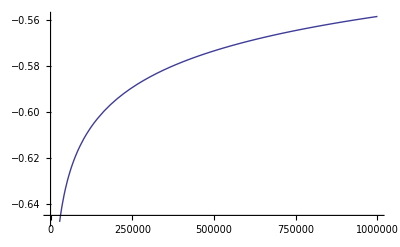

```mathematica
Plot[Re[Log[1-Log[x-1]]/Log[1-Log[1-Log[x-1]]]],{x,2,1000000}]
```

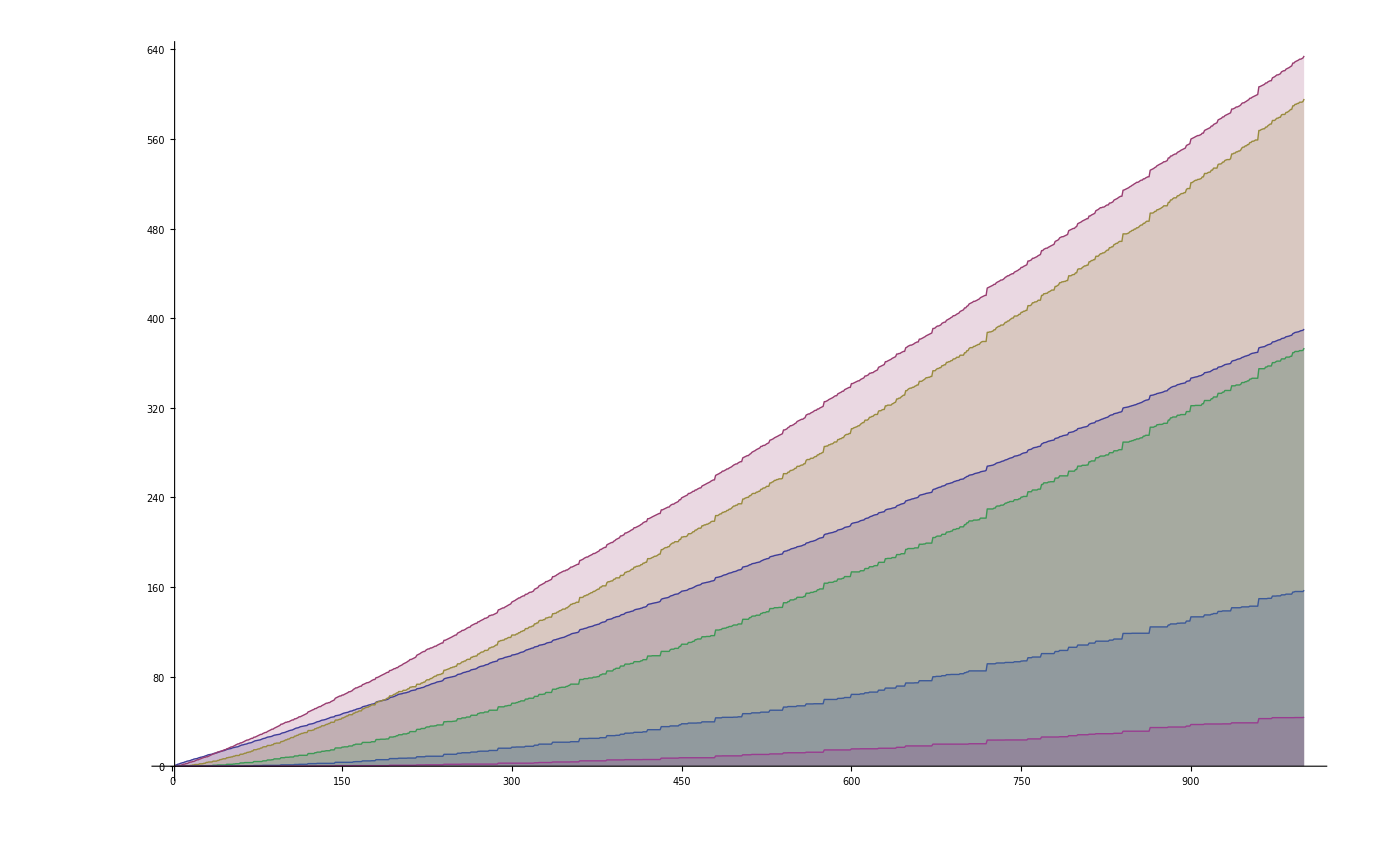

```mathematica
tx[p_]:=CoefficientList[Series[ (Log[x+1]/Log[1-Log[x+1]]+1)^p,{x,0,20}],x]
DiscretePlot[ {Sum[ tx[1][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[2][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[3][[k+1]] D2[n,k],{k,0,Log[2,n]}],
Sum[ tx[4][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[5][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[6][[k+1]] D2[n,k],{k,0,Log[2,n]}]},{n,2,1000}]
```

```mathematica
tx[5]
```

{0,0,0,0,0,1/32,-5/96,85/1152,-623/6912,2167/20736,-201995/1741824,2189227/17418240,-6984499/52254720,2445181/17418240,-1118775773/7664025600,145519551643/965667225600,-529483907749/3423729254400,5409067633031/34237292544000,-242225756635337/1506440871936000,163854164309879/1004293914624000,-2220202095423620309/13444984782028800000}

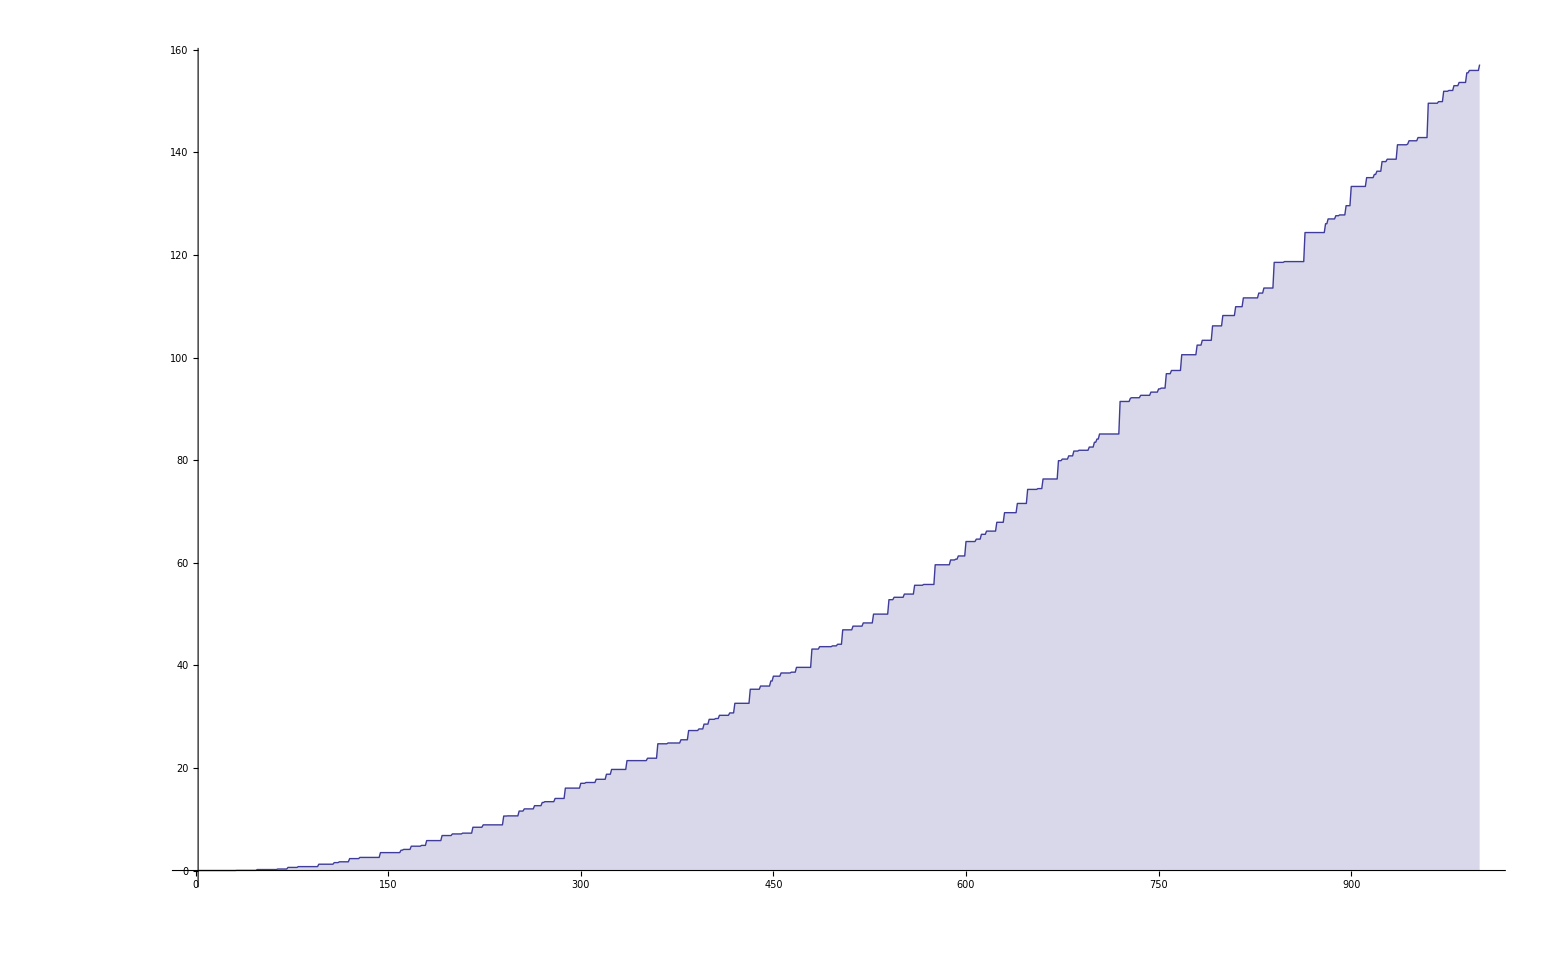

```mathematica
tx[p_]:=CoefficientList[Series[ (Log[x+1]/Log[1-Log[x+1]]+1)^p,{x,0,20}],x]
DiscretePlot[ {Sum[ tx[5][[k+1]] D2[n,k],{k,0,Log[2,n]}]},{n,2,1000}]
```

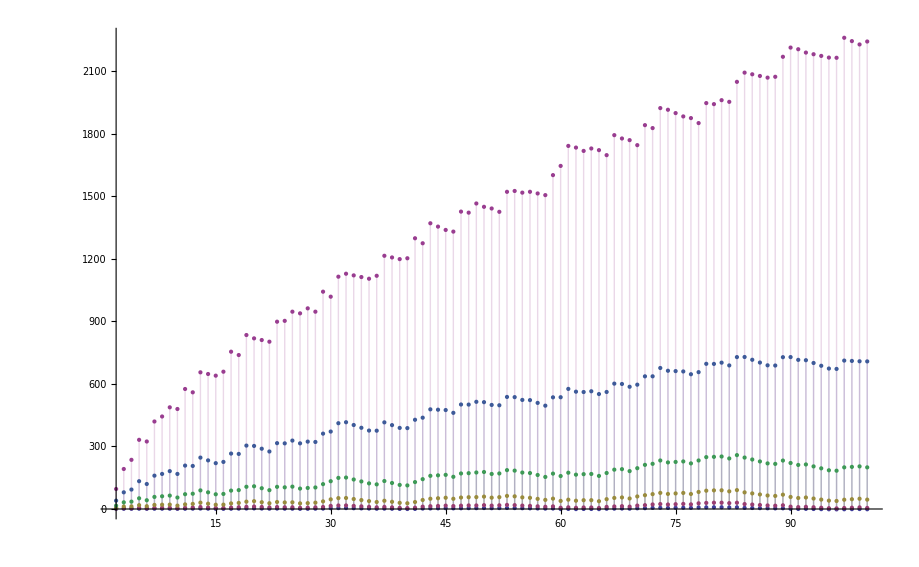

```mathematica
tx[p_]:=CoefficientList[Series[ (1+Log[1 + Log[1 + x]]/Log[1+Log[1+Log[1+x]]])^p,{x,0,20}],x]
DiscretePlot[ {Sum[ tx[1][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[2][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[3][[k+1]] D2[n,k],{k,0,Log[2,n]}],
Sum[ tx[4][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[5][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[6][[k+1]] D2[n,k],{k,0,Log[2,n]}]},{n,2,100}]
```

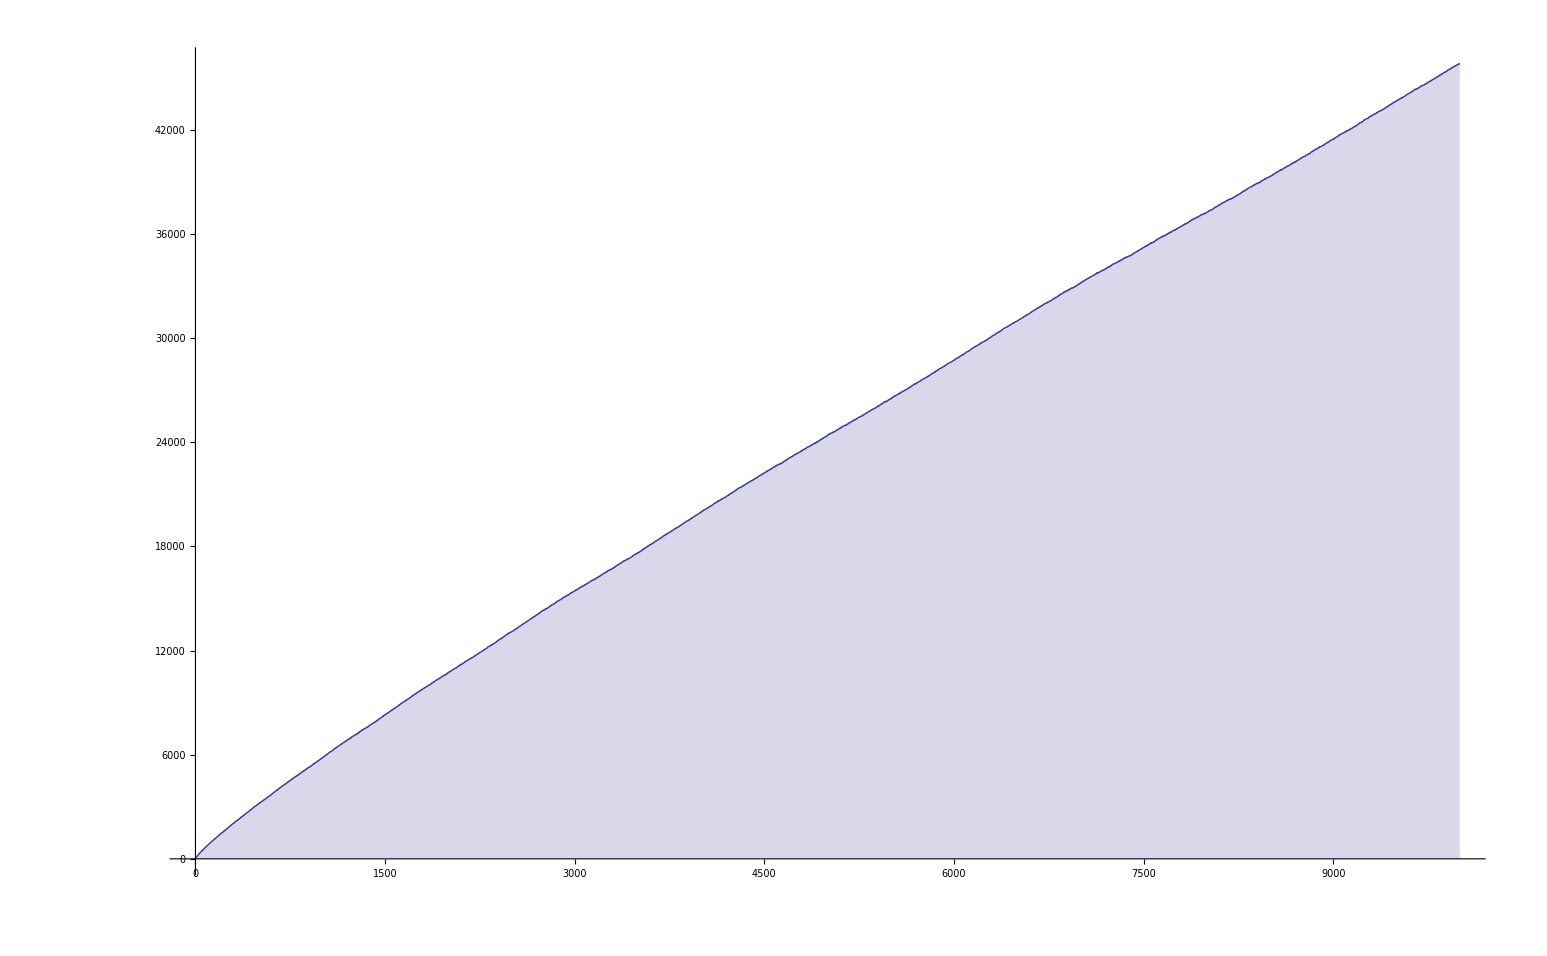

```mathematica
tx[p_]:=CoefficientList[Series[ (Log[x+1]/Log[1+Log[x+1]]+1)^p,{x,0,20}],x]
DiscretePlot[ {Sum[ tx[4][[k+1]] D2[n,k],{k,0,Log[2,n]}]},{n,1,10000}]
```

```mathematica
CoefficientList[Series[ (Log[x+1]/Log[1+Log[x+1]]-1)^4,{x,0,20}],x]
```

{0,0,0,0,1/16,-1/6,5/16,-2207/4320,40519/51840,-20959/18144,36504023/21772800,-13130779/5443200,1808060263/522547200,-7926004517/1596672000,1435964301661/201180672000,-161590944260929/15692092416000,28085912543626837/1883051089920000,-464199970130951/21398307840000,786750180754421/24831442944000,-120130716762724379/2585573996544000,5517399076532628998957/80669908692172800000}

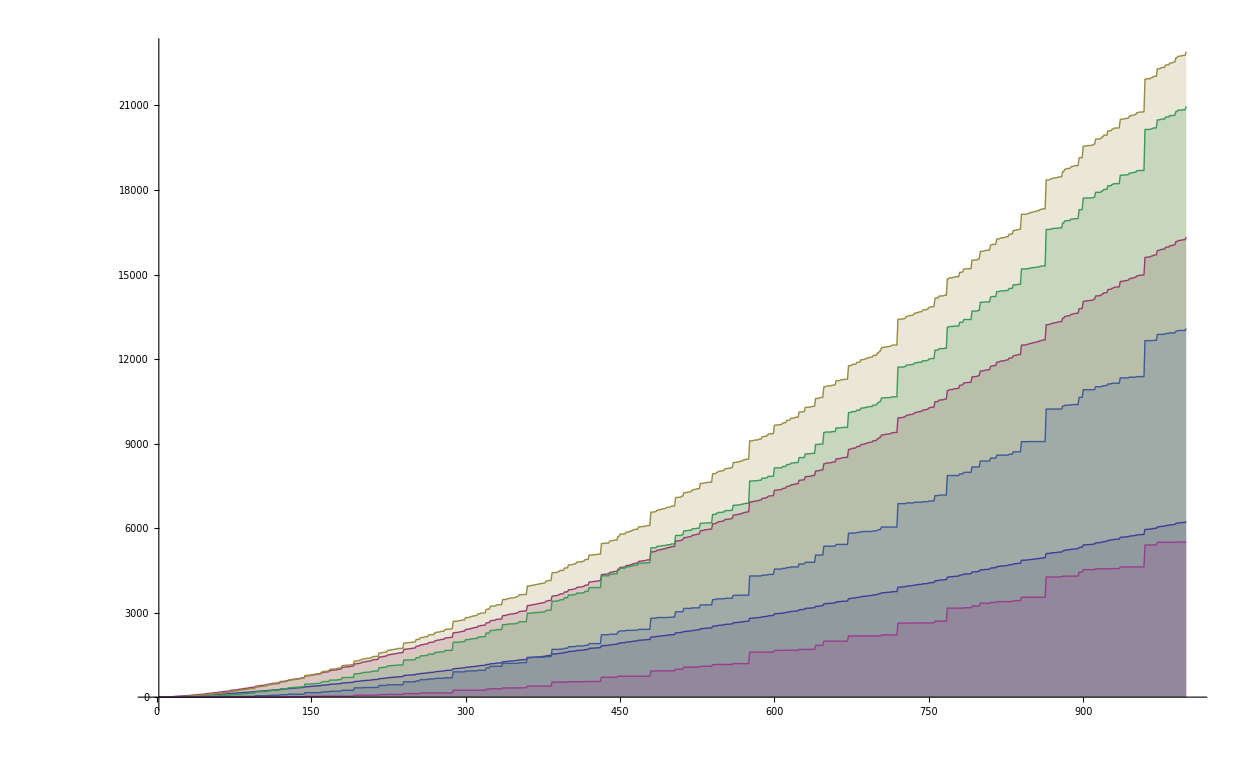

```mathematica
tx[p_]:=CoefficientList[Series[ (Tan[x])^p,{x,0,20}],x]
DiscretePlot[ {Sum[ tx[1][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[2][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[3][[k+1]] D2[n,k],{k,0,Log[2,n]}],
Sum[ tx[4][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[5][[k+1]] D2[n,k],{k,0,Log[2,n]}],Sum[ tx[6][[k+1]] D2[n,k],{k,0,Log[2,n]}]},{n,2,1000}]
```